```mathematica
raman, letting fSB vary
{{A->0.4791426828284226,f0->-1.450026935932844,Γ->9.389387002146421,B2->0.06268304875656606,B1->0.2087549814499051,A1->0.11707731664250498,Η2->8.182220446669659,Η1->15.110099585726042,Γ1->16.994029234136168,g2->-37.88686841730096,g1->-17.046211350806054,f1->17.90824548908818},
{0.02399212229719588,0.24263713923023128,1.0625976200401386,0.02381772416342585,0.017835223763307404,0.016200442268188515,5.341313971706681,3.134738674645458,4.266799241454805,1.4919353507100062,0.7968440145338228,1.3606468444805317}}

pgc, letting fSB vary
{A->0.4048147226716606,f0->-1.6671514929441127,Γ->7.739353163246676,B3->0.07947724907927294,B2->0.18969293580388683,B1->0.41501250899254505,A1->0.3605633002554282,A2->0.10457125752787916,A3->0.091162103569222,Η3->5.317547666611901,Η2->7.711135560396514,Η1->11.653258447195979,Γ1->10.55440159256723,Γ2->10.738244547756922,Γ3->9.076598907879337,g3->-56.628180156549575,g2->-37.50865158723932,g1->-19.04619679992402,f1->14.665848347058501,f2->33.001704763918895,f3->51.27004961219446},
{0.024819580967818777,0.2242686150058709,0.9663149748396404,0.02578008982474655,0.02486446781418942,0.01910688019306245,0.019954399299381528,0.019749455450971273,0.0211722819371422,2.764422602622283,1.7697228147883757,1.0874062797371453,1.1922400357702798,4.05681066126314,3.6190981862959983,1.206824530869687,0.4588943449940589,0.28839846497025146,0.32130423326125346,1.1083359640453525,1.1295982484093121}
```

```mathematica
Clear["Global`*"]
Needs["ErrorBarLogPlots`"]
kHz=10^3;nm=10^-9;mK=10^-3;uK=10^-6;us=10^-6;
kB=1.38064852 10^-23;ℏ=1.0545718 10^-34;amu=1.66054 10^-27;
m=132.90545 amu;λ=852nm;(*raman w/l*)ω=2π 18kHz;(*trap freq*)θ= ArcTan[10/11]; (*angle in rad b/t 2 axial raman beams*)
z0=√(ℏ/(2 m ω));η=Δk z0;k0=(2π)/λ;Δk=k0 Sin[θ];(*assuming the F3 beam has exactly 0 axial component*)√(2 k0^2(1-Cos[θ]))Sin[(π-θ)/2]; (*general expr*)

(*sbList:-ve = heating*)
{data,fittype,scaleList,nbarList,pCutoff,sbList}=
{"raman","area",Range[.7,1.5,.1],Range[2,15,1],.001,{-3,-2,-1,0,1,2,3}};
{"raman","area",Range[.8,1.2,.05],Range[.5,12,1],.001,{-1,0,1}};

{"raman","height",Range[.8,1.2,.05],Range[.5,12,1],.001,{-2,-1,1,2}};
{"raman","height",Range[.8,1.2,.05],Range[.5,12,1],.001,{-1,0,1}};

{"pgc","height",Range[.8,1.3,.1],Range[10,40,3],.001,{-3,-2,-1,0,1,2,3}};
{"pgc","area",Range[.8,1.2,.1],Range[13,40,2],.001,{-3,-2,-1,0,1,2,3}};

{"pgc","area",Range[.8,1.2,.1],Range[13,40,2],.001,{-2,-1,0,1,2}};
{"pgc","height",Range[.8,1.3,.1],Range[10,40,3],.001,{-2,-1,0,1,2}};

{"pgc","height",Range[.8,1.6,.1],Range[2,25,2],.001,{-2,-1,1,2}};
{"pgc","area",Range[.8,1.6,.2],Range[2,21,2],.001,{-2,-1,1,2}};
```

## data

```mathematica
(*parameter names dictionary*)
An={B3,B2,B1,A,A1,A2,A3}; (*sideband amplitudes from L to R, ie, heating Nth sb to cooling Nth sb*)
Γn={Η3,Η2,Η1,Γ, Γ1,Γ2,Γ3}; (*sideband FWHM from L to R*)
sbList0=Range[-#,#]&[(Length[An]-1)/2];(*index them with numbers, -n, ..0,...n*)
{fit,Δfit}=Switch[data,
"pgc",
(*fit parameters and errors for sidebands*){{A->0.39788397149439114,f0->-2.0003394224904363,Γ->8.617553675265427,B3->0.05160806532690174,B2->0.18155592285382477,B1->0.4132798356246277,A1->0.35368980017403034,A2->0.101172679590655,A3->0.08509569717076274,Η3->10.93882796013817,Η2->7.908129675016784,Η1->10.914957878226737,Γ1->11.080924262705086,Γ2->7.848594937114061,Γ3->12.111103850147819,fSB->17.370950284253652},{0.027065164665377856,0.19898514907995554,1.1261198079923553,0.02394239776244531,0.027761460669102008,0.023775658878614443,0.02336376004048464,0.0268309508562177,0.022677036639784348,9.655492403777602,2.2249573333021075,1.2239260571957875,1.4091169088020299,3.6327012751997714,5.775003711904422,0.19016300662166713}},
"raman",
(*fit parameters and errors for Raman sidebands*)
{{A->0.4850677177101539,f0->-1.42204072286107,Γ->9.727186040027956,B3->0.012957079002955115,B2->0.04014602284227754,B1->0.2030141999291329,A1->0.10312528189126294,A2->0.026816149053655352,A3->0.006543255000517483,Η3->33.22784358680099,Η2->9.038271674677167,Η1->13.98027916394115,Γ1->12.776036468217477,Γ2->18.789386944337565,Γ3->-95.32443757470273,fSB->16.598800649893903},{0.06021764855593731,0.2841296848726659,1.4738223327492945,0.05965687928123445,0.043283390744073384,0.06587178413593799,0.08409447861830774,0.02780175895596143,0.02531496351114545,223.28787785591973,14.305094841002578,4.993085200074373,11.698545723651854,47.3738954453149,3378.134768531989,0.7977760666987244}}

];
(*convert to ordered triplet: {fit param name, fit param Est, fit param Err}*)
fit=Thread[{fit[[;;,1]],fit[[;;,2]],Δfit}];

(*positions in fit corresponding to the A's  *)
Anpos=Flatten[Position[fit[[;;,1]],#]&/@An];
(*from fit, extract only the A's that were fitted.*)
Anfit=fit[[Anpos]];
(*replace all parameter names with sideband index. B1->-1 etc.*)
Anfit=Anfit/.(#1->#2&[An[[#]],sbList0[[#]]]&/@Range[Length[An]]);

(*repeat for Γ*)
Γnpos=Flatten[Position[fit[[;;,1]],#]&/@Γn];
Γnfit=fit[[Γnpos]];
Γnfit=Γnfit/.(#1->#2&[Γn[[#]],sbList0[[#]]]&/@Range[Length[Γn]]);

(*ordered triplet: {sbIndex, Psb(fit), ΔPsb(fit)}, for ALL the fitted sidebands. *)
fsb=Switch[fittype,
"height",
Anfit,

"area",
Thread[{
Anfit[[;;,1]],
Anfit[[;;,2]] Γnfit[[;;,2]],
√((Γ dA )^2+ (A dΓ)^2)/.{A->Anfit[[;;,2]],Γ->Γnfit[[;;,2]],dA->Anfit[[;;,3]],dΓ->Γnfit[[;;,3]]}
}]
];
(*normalization factor*)
totalfsb=Total[fsb[[;;,2]]];
fsb=Flatten[#]&/@Thread[{fsb[[;;,1]],fsb[[;;,{2,3}]]/totalfsb}];
```

## analytic

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of Solve :: ifun will be suppressed during this calculation.

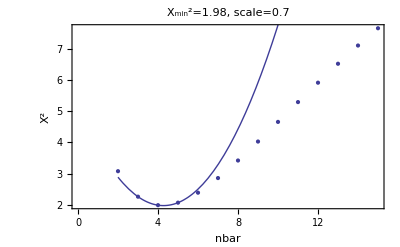

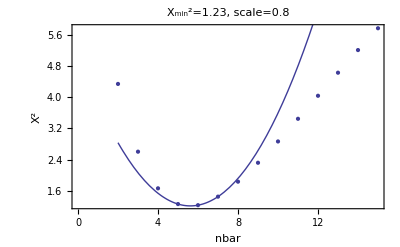

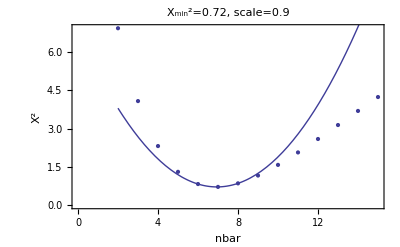

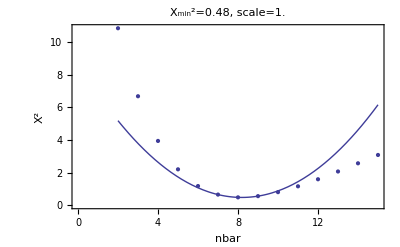

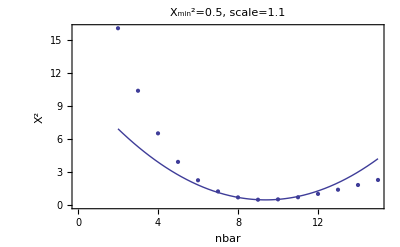

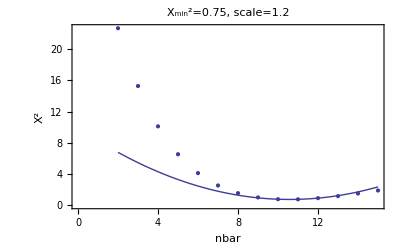

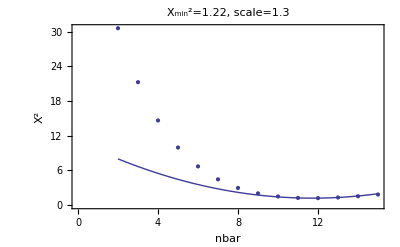

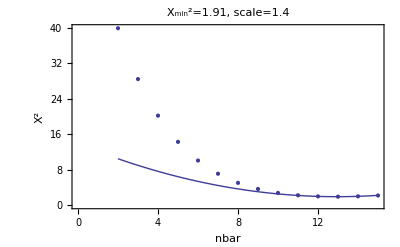

```mathematica
(*define the function for calculating sideband probs*)
PsbCalc[scale1_,nbar1_]:=
Module[{scale=scale1,nbar=nbar1},
(*sideband rabi freq/ΩR, ΩR~carrier rabi without lamb dicke. laguerre poly is in the hydrogen radial wavefunction*)
μ[m_,n_]:=Exp[-η^2/2] √((nMin!)/(nMax!))η^(nMax-nMin)LaguerreL[nMin,nMax-nMin,η^2]/.nMin->Min[m,n]/.nMax->Max[m,n];
(*thermal occupation probabilities*)
P[n_]:= nbar^n/(1+nbar)^(n+1);
nCutoff=Ceiling[n/.Solve[P[n]==pCutoff][[1,1]]];(*go until occupation prob drops to .001*) Ceiling[αn nbar]; (*how many harmonic oscillator levels to include*)

(*to get the nth order sideband, have to sum over ALL possible transitions of that order. weight factors: thermal occupation prob x matrix element (both depend on n)*)
HSB[order_]:=scale Sum[μ[n,n+order]^2 P[n],{n,0,nCutoff-order}];
CSB[order_]:=scale Sum[μ[n,n-order]^2 P[n],{n,order,nCutoff}];

(*this part is slow; defining fsbfit*)
hIndex=Cases[sbList,x_/;x<0];
cIndex=Cases[sbList,x_/;x>0];
(*what sideband indices to include?*)
hsb=Thread[{hIndex,HSB[#]&/@Abs[hIndex]}];
csb=Thread[{cIndex,CSB[#]&/@Abs[cIndex]}];
(*include carrier?*)
If[MemberQ[sbList,0],
carrier={{0,scale Sum[μ[n,n]^2 P[n],{n,0,nCutoff}]}};
fsbfit=Join[ hsb,carrier,csb],
fsbfit=Join[ hsb,csb]
];
chiSquare=Total[(#[[;;,2]]-fsbfit[[;;,2]])^2/(#[[;;,3]])^2&[Cases[fsb,x_/;MemberQ[sbList,x[[1]]]]]];
];
Χvsscale=Reap[
Do[

Χvsnbar=Reap[
Do[
PsbCalc[scale,nbar]
Sow[{nbar, chiSquare}]
,{nbar,nbarList}]
][[2,1]];

Χsquaremin=Min[Χvsnbar[[;;,2]]];
posBestFit=Position[Χvsnbar[[;;,2]],Χsquaremin][[1,1]];
nbarfitfn=a (x-x0)^2+b;
nlmnbar=NonlinearModelFit[Χvsnbar[[posBestFit-1;;posBestFit+1]],nbarfitfn,{a,{x0,Χvsnbar[[posBestFit,1]]},{b,Χsquaremin}},x];
nbarfit=nlmnbar["BestFitParameters"];
Print[Show[{
ListPlot[Χvsnbar,PlotLabel->"Χ_min^2="<>ToString[Round[Χsquaremin,.01]]<>", scale="<>ToString[scale],Axes->False,Frame->True,FrameLabel->{"nbar","Χ^2"}],
Plot[nbarfitfn/.nbarfit,{x,nbarList[[1]],nbarList[[-1]]}]}]];
Sow[{scale,b/.nbarfit(*Subscript[(Χ^2), min,fitted]*),√(a^-1)/.nbarfit(*std error in nbar*)}]
,{scale,scaleList}]][[2,1]];
```

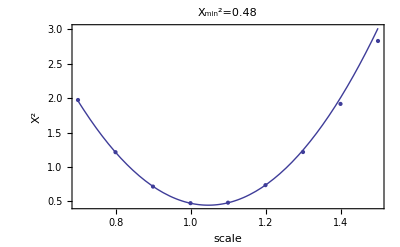

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of Solve :: ifun will be suppressed during this calculation.

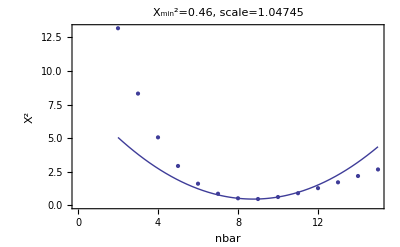

```mathematica
Χvsscale=DeleteCases[Χvsscale,x_/;Head[x[[2]]]==ReplaceAll];
Χsquaremin=Min[Χvsscale[[;;,2]]];
posBestFit=Position[Χvsscale[[;;,2]],Χsquaremin][[1,1]];
nbarErr=Χvsscale[[posBestFit,3]]; (*approx. error in nbar*)

scalefitfn=a (x-x0)^2+b;

nlmscale=NonlinearModelFit[Χvsscale[[posBestFit-2;;posBestFit+2,{1,2}]],scalefitfn,{a,{x0,Χvsscale[[posBestFit,1]]},{b,Χsquaremin}},x];
scalefit=nlmscale["BestFitParameters"];
Print[Show[{
ListPlot[Χvsscale[[;;,{1,2}]],PlotLabel->"Χ_min^2="<>ToString[Round[Χsquaremin,.01]],Axes->False,Frame->True,FrameLabel->{"scale","Χ^2"},PlotRange->All],
Plot[scalefitfn/.scalefit,{x,scaleList[[1]],scaleList[[-1]]}]}]];

Χvsnbar=Reap[
Do[
PsbCalc[x0/.scalefit,nbar]
Sow[{nbar, chiSquare}]
,{nbar,nbarList}]
][[2,1]];
Χsquaremin=Min[Χvsnbar[[;;,2]]];
posBestFit=Position[Χvsnbar[[;;,2]],Χsquaremin][[1,1]];
nbarfitfn=a (x-x0)^2+b;
nlmnbar=NonlinearModelFit[Χvsnbar[[posBestFit-1;;posBestFit+1]],nbarfitfn,{a,{x0,Χvsnbar[[posBestFit,1]]},{b,Χsquaremin}},x];
nbarfit=nlmnbar["BestFitParameters"];

Print[Show[{
ListPlot[Χvsnbar,PlotLabel->"Χ_min^2="<>ToString[Round[Χsquaremin,.01]]<>", scale="<>ToString[x0/.scalefit],Axes->False,Frame->True,FrameLabel->{"nbar","Χ^2"}],
Plot[nbarfitfn/.nbarfit,{x,nbarList[[1]],nbarList[[-1]]}]}]];
```

## plot

```mathematica
sbList
sbList=fsb[[;;,1]];
PsbCalc[x0/.scalefit,x0/.nbarfit]
TEst=(ℏ ω)/(kB Log[1/nbar+1] uK)/.nbar->(x0/.nbarfit);
Show[{
ListPlot[fsbfit,Joined->True,Axes->False,Frame->True,FrameLabel->{"sideband index","Σ_n(A_(n → m))^2P_n"},PlotStyle->Red,PlotRange->{All,{0,.65}},PlotLabel->" fit "<>fittype<>", "<>data<>", Χ_min^2="<>ToString[Round[chiSquare,0.1]]<>", nbar="<>ToString[Round[x0/.nbarfit,0.01]]<>"+/-"<>ToString[Round[nbarErr,0.1]]<>", T_est="<>ToString[Round[TEst,.1]]<>"uK"],

ErrorListPlot[Thread[{fsb⟦1;;All,{1,2}⟧,(ErrorBar[#1]&)/@fsb⟦1;;All,3⟧}],Axes->False,Frame->True]
}]
```

## fitting the area gives pathological behaviour--for no carrier, chisquare goes below .3, scale goes above 3, nbar goes below 2 for yes carrier, I get this:

{-3,-2,-1,0,1,2,3}

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

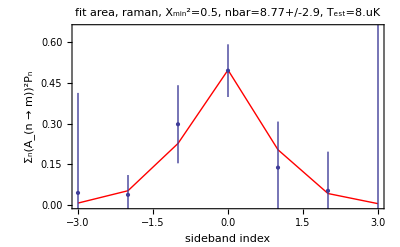

## fix fSB in fit--raman--height,

{-3,-2,-1,0,1,2,3}

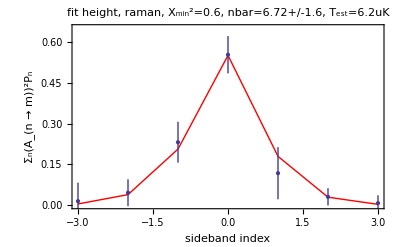

{-2,-1,0,1,2}

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

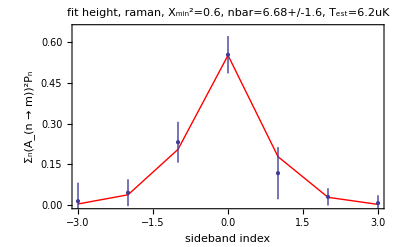

{-1,0,1}

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

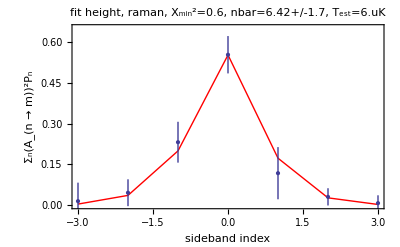

{-3,-2,-1,1,2,3}

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

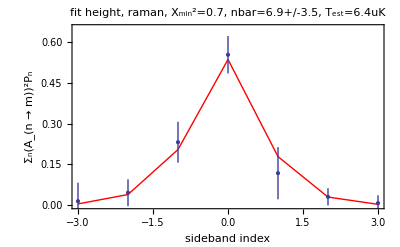

{-2,-1,1,2}

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

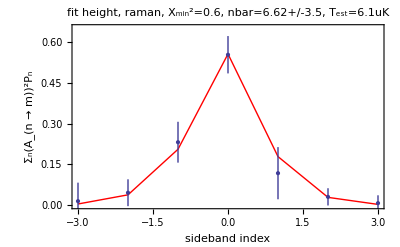

## fix fSB in fit--pgc--height, no carrier gives 15uK, yes carrier gives 20uK

{-3,-2,-1,0,1,2,3}

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

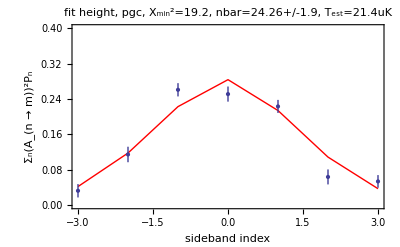

{-3,-2,-1,0,1,2,3}

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

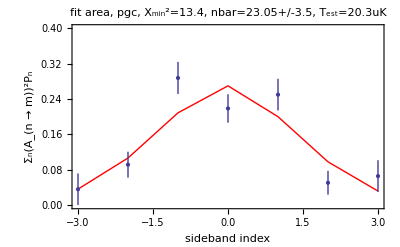

{-2,-1,0,1,2}

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

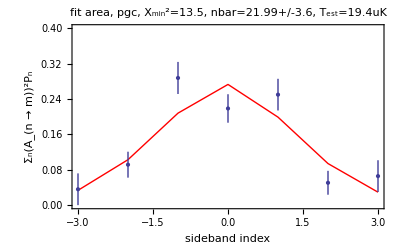

{-2,-1,0,1,2}

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

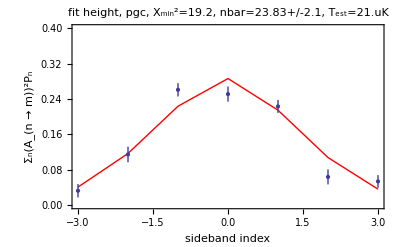

{-2,-1,1,2}

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

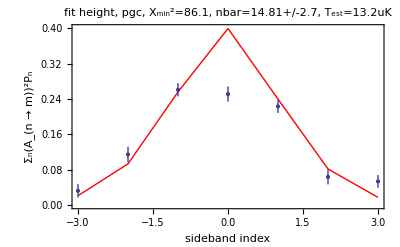

{-2,-1,1,2}

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

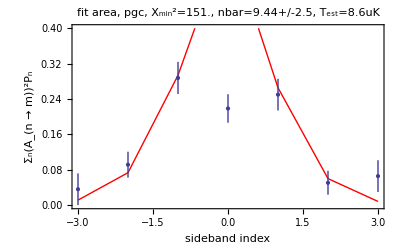

{-3,-2,-1,1,2,3}

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

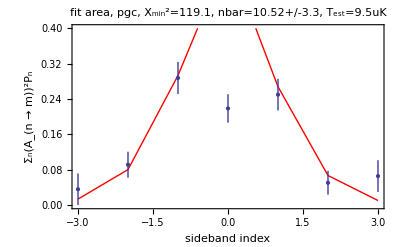

{-3,-2,-1,1,2,3}

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

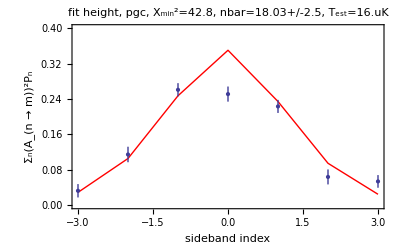

## save--vary fSB in fit

{-3,-2,-1,1,2,3}

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

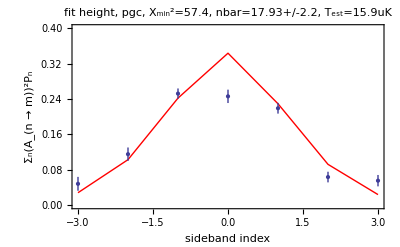

{-3,-2,-1,1,2,3}

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.